## Evolution of curves

### Initial curves

#### Curves generating function

```mathematica
Needs["DifferentialEquations`InterpolatingFunctionAnatomy`"];ClearSystemCache[];
```

```mathematica
curgen[num_,width_,height_,kink_,touch_,asymmetrie_,diagonaldistortion_]:=Module[{lo,initialcurve,aoi},
Subscript[te, num,0]=0;
initialcurve[u_]:=Exp[asymmetrie (Sin[u]-1)]({width (1-kink Cos[u]^2)(Sin[u]),height  (1-touch Cos[u]^2)(Cos[u])}+diagonaldistortion{Sin[u],Sin[u]});lo=NIntegrate[Sqrt[D[initialcurve[u], u].D[initialcurve[u], u]],{u,0,2π}];
aoi=-1/2 NIntegrate[(initialcurve[u][[1]])(D[initialcurve[u][[2]], u])-(initialcurve[u][[2]])( D[initialcurve[u][[1]], u]),{u,0,2π}];
Subscript[curve, num,0][u_]:=10initialcurve[u]/Sqrt[aoi/(2π)];
ParametricPlot[{Subscript[curve, num,0][u]},{u,0,2π}]];
```

```mathematica
Subscript[iao, num_]:=-1/2 NIntegrate[(Subscript[curve, num,0][u][[1]])(D[Subscript[curve, num,0][u][[2]], u])-(Subscript[curve, num,0][u][[2]])( D[Subscript[curve, num,0][u][[1]], u]),{u,0,2π}]
```

#### 1. curve

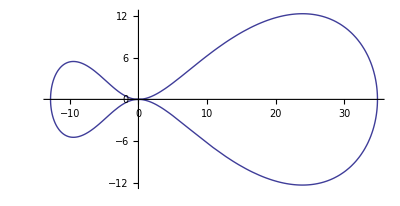

```mathematica
curgen[1,1,1,.4,1,.5,0]
```

#### 2. curve

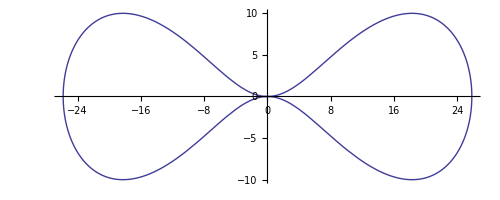

```mathematica
curgen[2,1,1,.4,1,0,0]
```

#### 3. curve

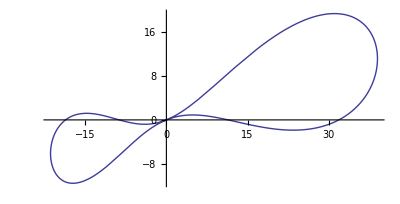

```mathematica
curgen[3,1,1,.4,1,0.3,.4]
```

#### 4. curve

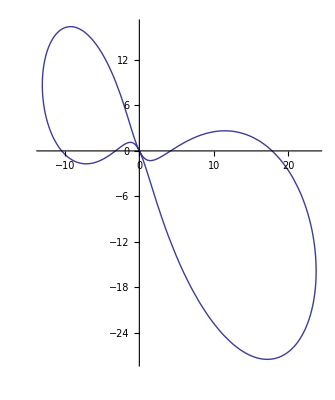

```mathematica
curgen[4,1,1,.4,1,0.3,-.4]
```

#### 5. curve

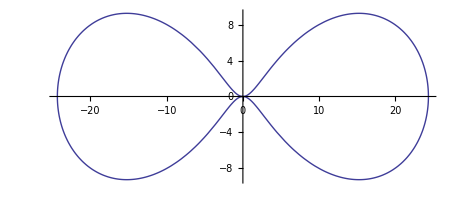

```mathematica
curgen[5,1,1,.7,1,0,0]
```

#### 6. curve

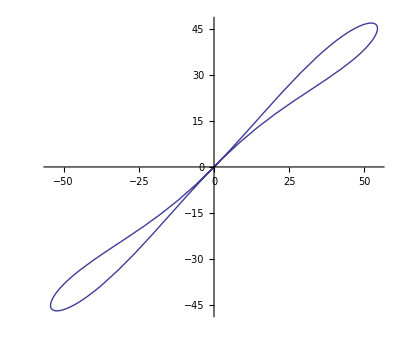

```mathematica
curgen[6,1,1.5,1,1,0,5]
```

### Functions

#### PDE, pbc, length functions

```mathematica
pdeinx =((D[x[u,t], u])^2+(D[y[u,t], u])^2)D[x[u,t], u,u]-(D[x[u,t], u]D[x[u,t], u,u]+D[y[u,t], u]D[y[u,t], u,u])D[x[u,t], u]-((D[x[u,t], u])^2+(D[y[u,t], u])^2)^2 D[x[u,t], t]==0; pdeiny=((D[x[u,t], u])^2+(D[y[u,t], u])^2)D[y[u,t], u,u]-(D[x[u,t], u]D[x[u,t], u,u]+D[y[u,t], u]D[y[u,t], u,u])D[y[u,t], u]-((D[x[u,t], u])^2+(D[y[u,t], u])^2)^2 D[y[u,t], t]==0; 
pbcinx=x[0,t]==x[2π,t] ;
pbciny=y[0,t]==y[2π,t];
clength[num_,step_]:=NIntegrate[Sqrt[(D[Subscript[curve, num,step][u], u]).(D[Subscript[curve, num,step][u], u])],{u,0,2π}];slength[num_,step_]:=NIntegrate[Sqrt[(D[x[u,Subscript[te, num,step]], u]/.Subscript[solution, num,step][[1,1]])^2+(D[y[u,Subscript[te, num,step]], u]/.Subscript[solution, num,step][[1,2]])^2],{u,0,2π}];
```

#### Evolution function

```mathematica
flow[num_,step_,tintervall_]:=Module[{time},
Subscript[te, num,step]=Subscript[te, num,step-1]+tintervall;
Subscript[stepstop, num]=step;
time=Timing[Subscript[solution, num,step]=
NDSolve[{ pdeinx, pdeiny,
x[0,t]==0,
y[0,t]==0,
x[u,Subscript[te, num,step-1]]==Subscript[curve, num,step-1][u][[1]],
y[u,Subscript[te, num,step-1]]==Subscript[curve, num,step-1][u][[2]]},
{x,y},{u,0,2π},{t,Subscript[te, num,step-1],Subscript[te, num,step]},
DependentVariables->{x,y},
InterpolationOrder->All,
Method->{"MethodOfLines",
"TemporalVariable"->t,
"SpatialDiscretization"->
{"TensorProductGrid",
DifferenceOrder->6,
MinPoints->100,
StartingPoints->100},
"DifferentiateBoundaryConditions"->True,
Method->Automatic,
Method->Automatic},
WorkingPrecision->MachinePrecision,
AccuracyGoal->Automatic,
PrecisionGoal->Automatic,
InterpolationOrder->Automatic,
SolveDelayed->False];];
If[step==1,
Subscript[sl, num,0]=NIntegrate[Sqrt[(D[x[u,0], u]/.Subscript[solution, num,1][[1,1]])^2+(D[y[u,0], u]/.Subscript[solution, num,1][[1,2]])^2],{u,0,2π}];
Subscript[ao, num]=-1/2 NIntegrate[(x[u,0]/.Subscript[solution, num,1][[1,1]])(D[y[u,0], u]/.Subscript[solution, num,1][[1,2]])-(y[u,0]/.Subscript[solution, num,1][[1,2]])( D[x[u,0], u]/.Subscript[solution, num,1][[1,1]]),{u,0,2π}];];
Print[num,". Kurve(",Subscript[ao, num]/(2π)"), ",step,". Evolution:   Laenge Anfangskurve = ",clength[num,step-1]," , Laenge nach Fluss = ",
Subscript[sl, num,step]=slength[num,step]," , Berechnungsdauer = ",time[[1]]]];

fgp[num_,step_,tintervall_]:=(flow[num,step,tintervall];grdplot[num,step]);
```

#### Plotting functions

```mathematica
flowplot[num_,step_]:=ParametricPlot3D[Evaluate[{x[u,t],y[u,t],20t}/. Subscript[solution, num,step]],{u,0,2π},{t,Subscript[te, num,step-1],Subscript[te, num,step]}];
grdplot[num_,step_]:=Module[{xso,yso,grdpts,GridPointPlot},
xso={Subscript[solution, num,step][[1,1]]};
yso={Subscript[solution, num,step][[1,2]]};
GridPointPlot[{x->xif_InterpolatingFunction},{y->yif_InterpolatingFunction}, t_, opts___] := Module[{xgrid = DifferentialEquations`InterpolatingFunctionAnatomy`InterpolatingFunctionCoordinates[xif][[1]]},
ListPlot[Transpose[{ xif[xgrid, t],yif[xgrid, t]}], opts]];
grdpts=
Map[Length,DifferentialEquations`InterpolatingFunctionAnatomy`InterpolatingFunctionCoordinates[x /. xso]][[1]]-1;
Print["Gitterpunkte von NUMOL: ",grdpts];
Show[
ListPlot[{Table[Subscript[curve, num,step-1][2Pi/grdpts i],{i,0,(grdpts-1)}]},PlotStyle->{Green,Opacity[.5],PointSize[Medium]}],
ListPlot[{Subscript[curve, num,step-1][0],Subscript[curve, num,step-1][π]},PlotStyle->{Magenta,PointSize[Large]}],
GridPointPlot[xso,yso,Subscript[te, num,step-1],PlotStyle->{Red,PointSize[Small]}],
GridPointPlot[xso,yso,Subscript[te, num,step],PlotStyle->{Blue,PointSize[Small]}],
PlotLabel->{Style[Subscript["curve", num,step-1],Green],Style[Subscript[" solution", num,step][Subscript[te, num,step-1]],Red],Style[Subscript[" solution", num,step][Subscript[te, num,step]],Blue]}]];
equiplot[num_,step_]:=Show[
ParametricPlot[{{x[u,Subscript[te, num,step]],y[u,Subscript[te, num,step]]}/. Subscript[solution, num,step]},{u,0,2π}],ListPlot[First[{x[u,Subscript[te, num,step]],y[u,Subscript[te, num,step]]}/. Subscript[solution, num,step]]/. Subscript[ulu, num,step],PlotRange->{{-.15,.15},{-.1,.1}}]];
evoplot[num_]:=Block[{stretch=1},
Show[Table[ParametricPlot3D[{Evaluate[{x[u,t],y[u,t],stretch t}/. Subscript[solution, num,i]],{0,0,0}},{u,0,2π},{t,Subscript[te, num,i-1],Subscript[te, num,i]},PlotPoints->{30,10},Mesh->None],{i,Subscript[stepstop, num],1,-1}],PlotRange->All]];
```

#### Fitting functions

```mathematica
equidist[num_,step_,fitpts_,opts___]:=Module[{length,l,L,usol,time},
Subscript[numberoffitpts, num,step]=fitpts;
length=slength[num,step];
l[i_]:=length i/fitpts;
L[u_?NumberQ]:=NIntegrate[Sqrt[(D[Evaluate[x[p,Subscript[te, num,step]]/.Subscript[solution, num,step][[1,1]]], p])^2+(D[Evaluate[y[p,Subscript[te, num,step]]/.Subscript[solution, num,step][[1,2]]], p])^2],{p,0,u},opts];
usol[i_]:=FindRoot[L[u]==l[i],{u,0,2Pi}];
time=Timing[Subscript[ulu, num,step]=Table[usol[i],{i,0,fitpts}]];
Print["u-Bestimmungsdauer: ",time[[1]]];];
fit[num_,step_,order_]:=Module[{fitpts,xpts,ypts,xexp,yexp,xfk,yfk,xpara,ypara,yfitdat,xfitdat,cl},
fitpts=Subscript[numberoffitpts, num,step];
xpts=Table[{2Pi i/fitpts,x[u,Subscript[te, num,step]]/.Subscript[solution, num,step][[1,1]]/.Subscript[ulu, num,step][[i+1]]},{i,0,fitpts}];
ypts=Table[{2Pi i/fitpts,y[u,Subscript[te, num,step]]/.Subscript[solution, num,step][[1,2]]/.Subscript[ulu, num,step][[i+1]]},{i,0,fitpts}];
xexp[u_]:=Sum[Subscript[xfk, i] Cos[i u]+Subscript[xfk, order+i] Sin[i u],{i,0,order}];
yexp[u_]:=Sum[Subscript[yfk, i] Cos[i u]+Subscript[yfk, order+i] Sin[i u],{i,0,order}];
xpara=Table[Subscript[xfk, i] ,{i,0,2 order}];
ypara=Table[Subscript[yfk, i] ,{i,0,2 order}];
xfitdat=FindFit[xpts,xexp[u],xpara ,u];
yfitdat=FindFit[ypts,yexp[u],ypara ,u];
Subscript[curve, num,step][u_]:={xexp[u]/.xfitdat,yexp[u]/.yfitdat};
cl=clength[num,step];
Print[num,". Kurve, ",step,". Fit: Laenge nach Fluss = ",Subscript[sl, num,step]," , Laenge nach Fit = ",cl," , Abweichung = ",Abs[Subscript[sl, num,step]-cl]/Subscript[sl, num,step] 100"%"]]
```

#### Function over entire t-interval of coordinates, length, area. Plotting functions

```mathematica
Subscript[xevo, num_][u_,t_]:=Piecewise[Table[{x[u,t]/.Subscript[solution, num,i][[1,1]],Subscript[te, num,i-1]≤t≤Subscript[te, num,i]},{i,1,Subscript[stepstop, num]}],0];
Subscript[yevo, num_][u_,t_]:=Piecewise[Table[{y[u,t]/.Subscript[solution, num,i][[1,2]],Subscript[te, num,i-1]≤t≤Subscript[te, num,i]},{i,1,Subscript[stepstop, num]}],0];
Subscript[length, num_][t_]:=NIntegrate[Sqrt[(D[Subscript[xevo, num][u,t], u])^2+(D[Subscript[yevo, num][u,t], u])^2],{u,0,2π}];
Subscript[area, num_][t_]:=-1/2 NIntegrate[Subscript[xevo, num][u,t] (D[Subscript[yevo, num][u,t], u])-Subscript[yevo, num][u,t]( D[Subscript[xevo, num][u,t], u]),{u,0,2π}];
Subscript[lplot, num_]:=Show[
Plot[{Subscript[length, num][t]},{t,0,Subscript[te, num,Subscript[stepstop, num]]},PlotStyle->Blue],
ListPlot[Table[{Subscript[te, num,i],Subscript[sl, num,i]},{i,0,Subscript[stepstop, num]}],PlotStyle->{PointSize[Large],Green,Opacity[.5]}]];
Subscript[aplot, num_]:=Plot[Subscript[area, num][t],{t,0,Subscript[te, num,Subscript[stepstop, num]]},PlotRange-> Full];
Subscript[isoplot, num_]:=Plot[{Subscript[length, num][t]^2/Subscript[area, num][t],4π},{t,0,Subscript[te, num,Subscript[stepstop, num]]},PlotStyle->Red];
```

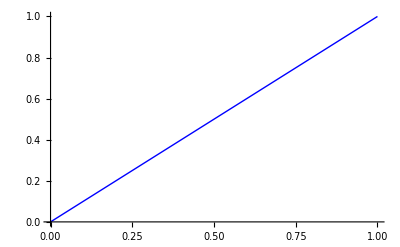

```mathematica
Plot[x,{x,0,1},PlotStyle->Blue]
```

### Evolution

#### 1. curve

NDSolve::bcart: Warning: An insufficient number of boundary conditions have been specified for the direction of independent variable u. Artificial boundary effects may be present in the solution.

1. Kurve(100. ), 1. Evolution:   Laenge Anfangskurve = 128.037 , Laenge nach Fluss = 120.73 , Berechnungsdauer = 0.080006

Gitterpunkte von NUMOL: 100

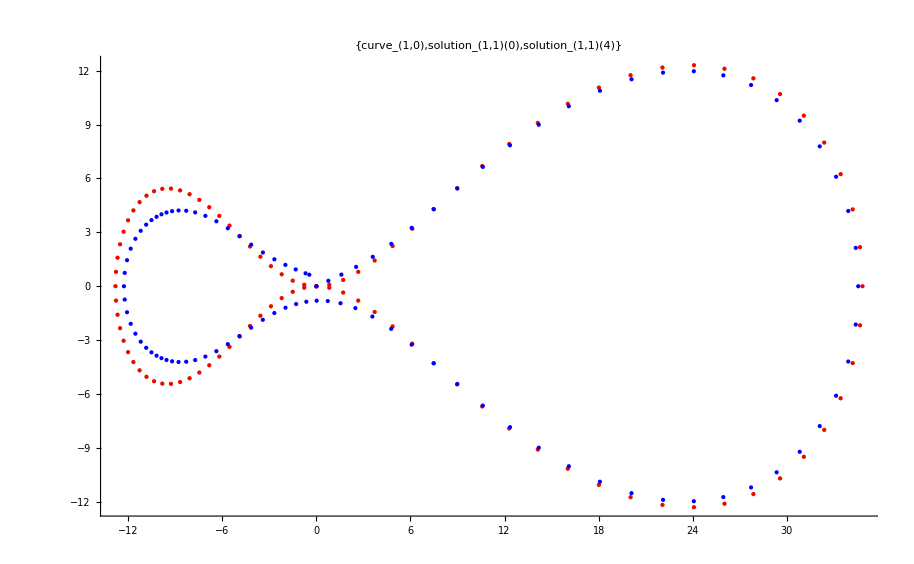

```mathematica
fgp[1,1,4]
```

```mathematica
Show[
ParametricPlot3D[{Evaluate[{x[u,0],y[u,0],0}/. Subscript[solution, 1,1]],{0,0,Subscript[te, 1,1]}},{u,0,2Pi},PlotRange->Full],
ParametricPlot3D[{Evaluate[{x[u,Subscript[te, 1,1]],y[u,Subscript[te, 1,1]],Subscript[te, 1,1]}/. Subscript[solution, 1,1]],{0,0,0}},{u,0,2Pi},PlotRange->Full],
ParametricPlot3D[{{Evaluate[{x[0,t],y[0,t], t}/. Subscript[solution, 1,1]],Evaluate[{x[Pi,t],y[Pi,t], t}/. Subscript[solution, 1,1]]},{Evaluate[{x[Pi/2,t],y[Pi/2,t], t}/. Subscript[solution, 1,1]],Evaluate[{x[3Pi/2,t],y[3Pi/2,t], t}/. Subscript[solution, 1,1]]}},{t,0,Subscript[te, 1,1]},PlotStyle->{Blue,Green}]
]
```

-Graphics3D-

```mathematica
equidist[1,1,50]
```

u-Bestimmungsdauer: 29.7499

```mathematica
fit[1,1,15];
```

1. Kurve, 1. Fit: Laenge nach Fluss = 106.574 , Laenge nach Fit = 106.543 , Abweichung = 0.0295027 %

1. Kurve(100. ), 2. Evolution:   Laenge Anfangskurve = 106.543 , Laenge nach Fluss = 97.8127 , Berechnungsdauer = 0.120007

Gitterpunkte von NUMOL: 100

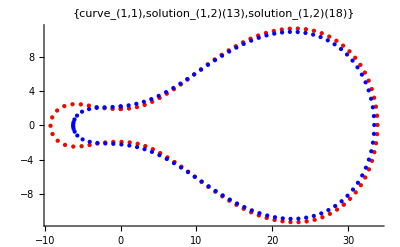

```mathematica
flow[1,2,5];grdplot[1,2]
```

```mathematica
equidist[1,2,90]
```

u-Bestimmungsdauer: 58.5797

```mathematica
fit[1,2,9]
```

1. Kurve, 2. Fit: Laenge nach Fluss: 75.1676 , Laenge nach Fit: 75.163 , Abweichung: 0.00613538 %

1. Kurve(100.), 3. Evolution:   Laenge Anfangskurve = 75.163 , Laenge nach Fluss = 25.1291 , Berechnungsdauer = 0.132009

Gitterpunkte von NUMOL: 100

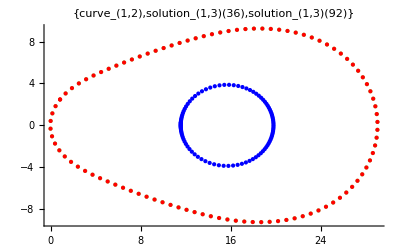

```mathematica
flow[1,3,56];grdplot[1,3]
```

```mathematica
equidist[1,3,80]
```

u-Bestimmungsdauer: 51.3472

```mathematica
fit[1,3,3]
```

1. Kurve, 3. Fit: Laenge nach Fluss: 25.1291 , Laenge nach Fit: 25.1293 , Abweichung: 0.000670589 %

1. Kurve(100.), 4. Evolution:   Laenge Anfangskurve = 25.1293 , Laenge nach Fluss = 7.30418 , Berechnungsdauer = 0.056004

Gitterpunkte von NUMOL: 100

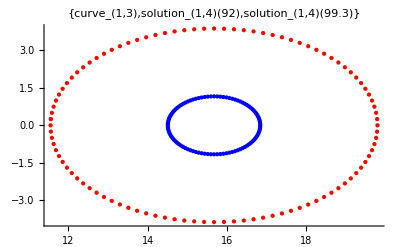

```mathematica
flow[1,4,7.3];grdplot[1,4]
```

```mathematica
equidist[1,4,50];
```

u-Bestimmungsdauer: 22.2494

```mathematica
fit[1,4,2]
```

1. Kurve, 4. Fit: Laenge nach Fluss: 7.30418 , Laenge nach Fit: 7.30425 , Abweichung: 0.00100307 %

1. Kurve(100.), 5. Evolution:   Laenge Anfangskurve = 7.30425 , Laenge nach Fluss = 2.5806 , Berechnungsdauer = 0.056003

Gitterpunkte von NUMOL: 100

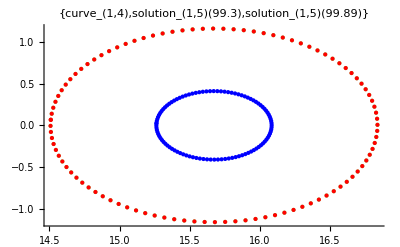

```mathematica
flow[1,5,.59];grdplot[1,5]
```

```mathematica
equidist[1,5,40]
```

u-Bestimmungsdauer: 14.9569

```mathematica
fit[1,5,1]
```

1. Kurve, 5. Fit: Laenge nach Fluss: 2.5806 , Laenge nach Fit: 2.5806 , Abweichung: 0.00014392 %

1. Kurve(100.), 6. Evolution:   Laenge Anfangskurve = 2.5806 , Laenge nach Fluss = 0.697025 , Berechnungsdauer = 0.068005

Gitterpunkte von NUMOL: 100

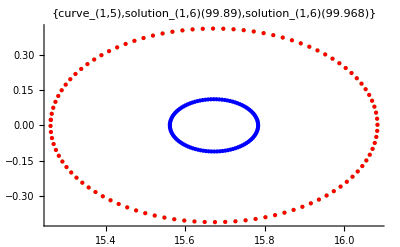

```mathematica
flow[1,6,.078];grdplot[1,6]
```

```mathematica
equidist[1,6,20]
```

u-Bestimmungsdauer: 7.62047

```mathematica
fit[1,6,1]
```

1. Kurve, 6. Fit: Laenge nach Fluss: 0.697025 , Laenge nach Fit: 0.697025 , Abweichung: 0.0000938317 %

1. Kurve(100.), 7. Evolution:   Laenge Anfangskurve = 0.697025 , Laenge nach Fluss = 0.369804 , Berechnungsdauer = 0.048003

Gitterpunkte von NUMOL: 100

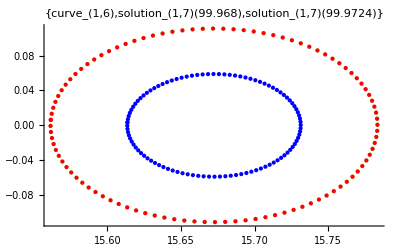

```mathematica
flow[1,7,.0044];grdplot[1,7]
```

```mathematica
equidist[1,7,20]
```

u-Bestimmungsdauer: 6.25239

```mathematica
fit[1,7,1]
```

1. Kurve, 7. Fit: Laenge nach Fluss: 0.369804 , Laenge nach Fit: 0.369803 , Abweichung: 0.00023064 %

1. Kurve(100.), 8. Evolution:   Laenge Anfangskurve = 0.369803 , Laenge nach Fluss = 0.0957677 , Berechnungsdauer = 0.052004

Gitterpunkte von NUMOL: 100

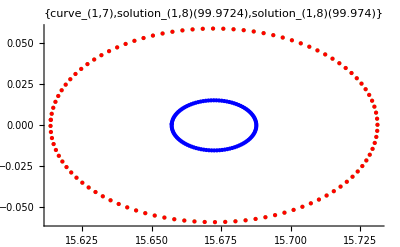

```mathematica
flow[1,8,.001585];grdplot[1,8]
```

```mathematica
equidist[1,8,20]
```

u-Bestimmungsdauer: 6.32039

```mathematica
fit[1,8,1]
```

1. Kurve, 8. Fit: Laenge nach Fluss: 0.0957677 , Laenge nach Fit: 0.0957677 , Abweichung: 2.06583×10^-6 %

1. Kurve(100.), 9. Evolution:   Laenge Anfangskurve = 0.0957677 , Laenge nach Fluss = 0.0627594 , Berechnungsdauer = 0.052004

Gitterpunkte von NUMOL: 100

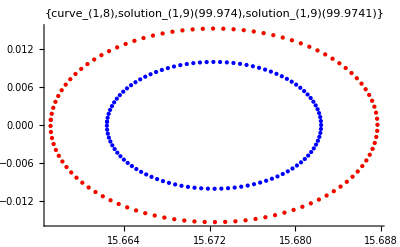

```mathematica
flow[1,9,.000066];grdplot[1,9]
```

#### 2. curve

2. Kurve(100.), 1. Evolution:   Laenge Anfangskurve = 125.675 , Laenge nach Fluss = 47.2301 , Berechnungsdauer = 0.15601

Gitterpunkte von NUMOL: 100

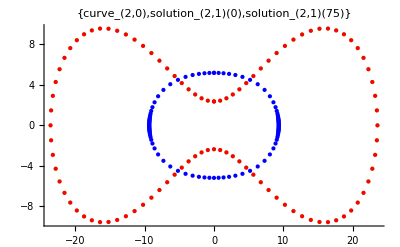

```mathematica
fgp[2,1,75]
```

```mathematica
equidist[2,1,60]
```

u-Bestimmungsdauer: 49.4151

```mathematica
fit[2,1,7]
```

2. Kurve, 1. Fit: Laenge nach Fluss: 47.2301 , Laenge nach Fit: 47.23 , Abweichung: 0.000300444 %

2. Kurve(100.), 2. Evolution:   Laenge Anfangskurve = 47.23 , Laenge nach Fluss = 25.3097 , Berechnungsdauer = 0.056003

Gitterpunkte von NUMOL: 100

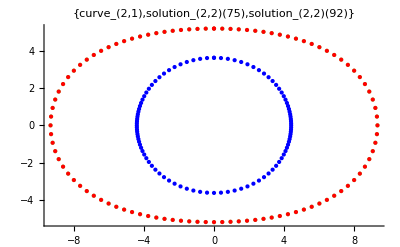

```mathematica
fgp[2,2,17]
```

```mathematica
equidist[2,2,40];
```

u-Bestimmungsdauer: 20.4133

```mathematica
fit[2,2,7]
```

2. Kurve, 2. Fit: Laenge nach Fluss: 25.3097 , Laenge nach Fit: 25.3096 , Abweichung: 0.00033847 %

2. Kurve(100.), 3. Evolution:   Laenge Anfangskurve = 25.3096 , Laenge nach Fluss = 7.88895 , Berechnungsdauer = 0.068004

Gitterpunkte von NUMOL: 100

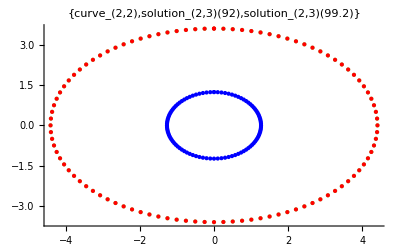

```mathematica
fgp[2,3,7.2]
```

```mathematica
equidist[2,3,40];
```

u-Bestimmungsdauer: 19.4412

```mathematica
fit[2,3,3]
```

2. Kurve, 3. Fit: Laenge nach Fluss: 7.88895 , Laenge nach Fit: 7.88895 , Abweichung: 0.0000199562 %

2. Kurve(100.), 4. Evolution:   Laenge Anfangskurve = 7.88895 , Laenge nach Fluss = 3.40596 , Berechnungsdauer = 0.060004

Gitterpunkte von NUMOL: 100

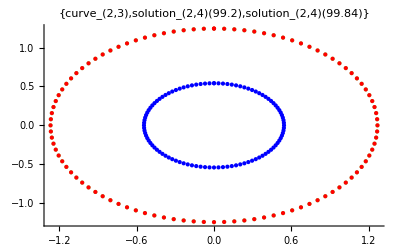

```mathematica
fgp[2,4,.64]
```

```mathematica
equidist[2,4,40]
```

u-Bestimmungsdauer: 15.417

```mathematica
fit[2,4,3]
```

2. Kurve, 4. Fit: Laenge nach Fluss: 3.40596 , Laenge nach Fit: 3.40596 , Abweichung: 4.67145×10^-6 %

2. Kurve(100.), 5. Evolution:   Laenge Anfangskurve = 3.40596 , Laenge nach Fluss = 0.718338 , Berechnungsdauer = 0.064004

Gitterpunkte von NUMOL: 100

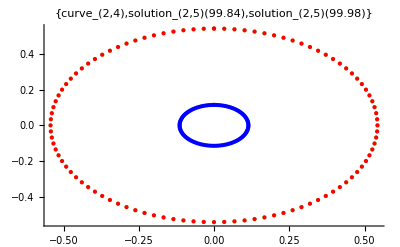

```mathematica
fgp[2,5,.14]
```

```mathematica
equidist[2,5,20]
```

u-Bestimmungsdauer: 7.18845

```mathematica
fit[2,5,1]
```

2. Kurve, 5. Fit: Laenge nach Fluss: 0.718338 , Laenge nach Fit: 0.718338 , Abweichung: 0.0000937615 %

2. Kurve(100.), 6. Evolution:   Laenge Anfangskurve = 0.718338 , Laenge nach Fluss = 0.398491 , Berechnungsdauer = 0.044002

Gitterpunkte von NUMOL: 100

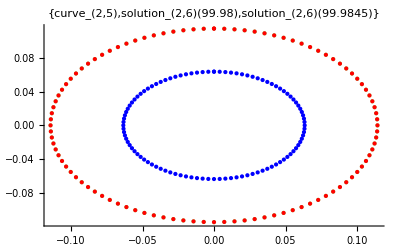

```mathematica
fgp[2,6,.00445]
```

```mathematica
equidist[2,6,20]
```

u-Bestimmungsdauer: 6.01238

```mathematica
fit[2,6,1]
```

2. Kurve, 6. Fit: Laenge nach Fluss: 0.398491 , Laenge nach Fit: 0.398491 , Abweichung: 0.0000217858 %

2. Kurve(100.), 7. Evolution:   Laenge Anfangskurve = 0.398491 , Laenge nach Fluss = 0.0109139 , Berechnungsdauer = 0.132008

Gitterpunkte von NUMOL: 100

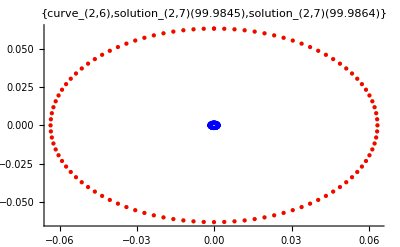

```mathematica
fgp[2,7,.001979]
```

#### 3. curve

3. Kurve(100.), 1. Evolution:   Laenge Anfangskurve = 125.655 , Laenge nach Fluss = 104.941 , Berechnungsdauer = 0.080005

Gitterpunkte von NUMOL: 100

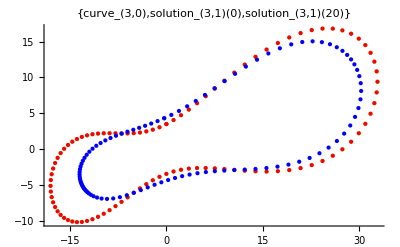

```mathematica
fgp[3,1,20]
```

```mathematica
equidist[3,1,100]
```

u-Bestimmungsdauer: 56.9876

```mathematica
fit[3,1,16]
```

3. Kurve, 1. Fit: Laenge nach Fluss: 104.941 , Laenge nach Fit: 104.94 , Abweichung: 0.000638525 %

3. Kurve(100.), 2. Evolution:   Laenge Anfangskurve = 104.94 , Laenge nach Fluss = 83.8071 , Berechnungsdauer = 0.140009

Gitterpunkte von NUMOL: 100

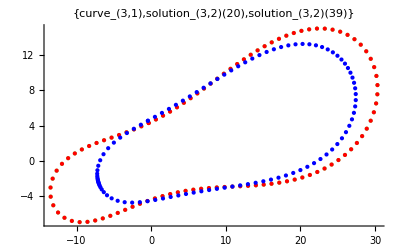

```mathematica
fgp[3,2,19]
```

```mathematica
equidist[3,2,100]
```

u-Bestimmungsdauer: 67.9002

```mathematica
fit[3,2,16]
```

3. Kurve, 2. Fit: Laenge nach Fluss: 83.8071 , Laenge nach Fit: 83.8068 , Abweichung: 0.000433597 %

3. Kurve(100.), 3. Evolution:   Laenge Anfangskurve = 83.8068 , Laenge nach Fluss = 62.6659 , Berechnungsdauer = 0.120008

Gitterpunkte von NUMOL: 100

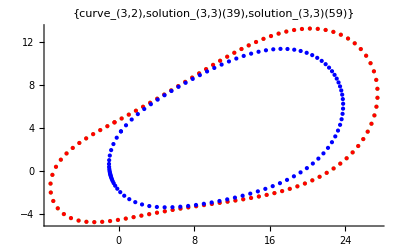

```mathematica
fgp[3,3,20]
```

```mathematica
equidist[3,3,80]
```

u-Bestimmungsdauer: 53.2873

```mathematica
fit[3,3,10]
```

3. Kurve, 3. Fit: Laenge nach Fluss: 62.6659 , Laenge nach Fit: 62.6654 , Abweichung: 0.000776778 %

3. Kurve(100.), 4. Evolution:   Laenge Anfangskurve = 62.6654 , Laenge nach Fluss = 28.294 , Berechnungsdauer = 0.120008

Gitterpunkte von NUMOL: 100

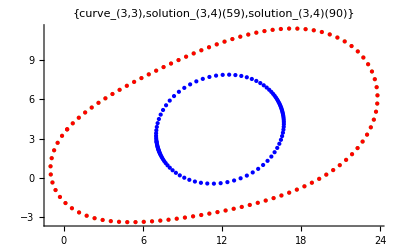

```mathematica
fgp[3,4,31]
```

```mathematica
equidist[3,4,60]
```

u-Bestimmungsdauer: 41.6946

```mathematica
fit[3,4,3]
```

3. Kurve, 4. Fit: Laenge nach Fluss: 28.294 , Laenge nach Fit: 28.294 , Abweichung: 8.82018×10^-6 %

3. Kurve(100.), 5. Evolution:   Laenge Anfangskurve = 28.294 , Laenge nach Fluss = 14.1835 , Berechnungsdauer = 0.068004

Gitterpunkte von NUMOL: 100

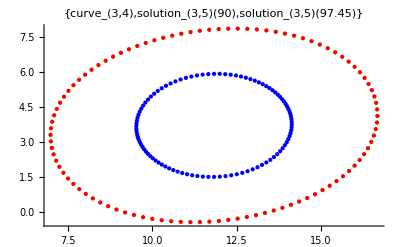

```mathematica
fgp[3,5,7.45]
```

```mathematica
equidist[3,5,40]
```

u-Bestimmungsdauer: 18.3651

```mathematica
fit[3,5,3]
```

3. Kurve, 5. Fit: Laenge nach Fluss: 14.1835 , Laenge nach Fit: 14.1835 , Abweichung: 0.0000985603 %

3. Kurve(100.), 6. Evolution:   Laenge Anfangskurve = 14.1835 , Laenge nach Fluss = 5.66283 , Berechnungsdauer = 0.056004

Gitterpunkte von NUMOL: 100

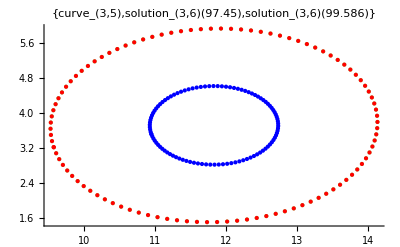

```mathematica
fgp[3,6,2.13599]
```

```mathematica
equidist[3,6,20]
```

u-Bestimmungsdauer: 8.44053

```mathematica
fit[3,6,3]
```

3. Kurve, 6. Fit: Laenge nach Fluss: 5.66283 , Laenge nach Fit: 5.66283 , Abweichung: 0.0000283856 %

3. Kurve(100.), 7. Evolution:   Laenge Anfangskurve = 5.66283 , Laenge nach Fluss = 2.00842 , Berechnungsdauer = 0.056004

Gitterpunkte von NUMOL: 100

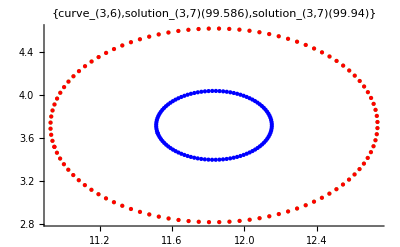

```mathematica
fgp[3,7,.354]
```

```mathematica
equidist[3,7,20]
```

u-Bestimmungsdauer: 8.31252

```mathematica
fit[3,7,3]
```

3. Kurve, 7. Fit: Laenge nach Fluss: 2.00842 , Laenge nach Fit: 2.00842 , Abweichung: 0.0000977261 %

3. Kurve(100.), 8. Evolution:   Laenge Anfangskurve = 2.00842 , Laenge nach Fluss = 0.0914559 , Berechnungsdauer = 0.088005

Gitterpunkte von NUMOL: 100

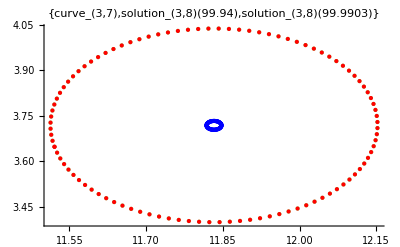

```mathematica
fgp[3,8,.0503]
```

#### 4. curve

4. Kurve(100.), 1. Evolution:   Laenge Anfangskurve = 115.761 , Laenge nach Fluss = 78.9025 , Berechnungsdauer = 0.176011

Gitterpunkte von NUMOL: 100

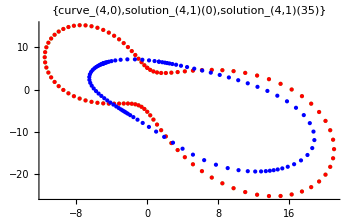

```mathematica
fgp[4,1,35]
```

```mathematica
equidist[4,1,100]
```

u-Bestimmungsdauer: 94.1259

```mathematica
fit[4,1,12]
```

4. Kurve, 1. Fit: Laenge nach Fluss: 78.9025 , Laenge nach Fit: 78.9025 , Abweichung: 0.0000290521 %

4. Kurve(100.), 2. Evolution:   Laenge Anfangskurve = 78.9025 , Laenge nach Fluss = 32.1812 , Berechnungsdauer = 0.164011

Gitterpunkte von NUMOL: 100

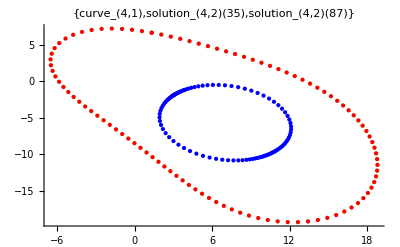

```mathematica
fgp[4,2,52]
```

```mathematica
equidist[4,2,60]
```

u-Bestimmungsdauer: 50.3871

```mathematica
fit[4,2,13]
```

4. Kurve, 2. Fit: Laenge nach Fluss: 32.1812 , Laenge nach Fit: 32.1812 , Abweichung: 0.0000862097 %

4. Kurve(100.), 3. Evolution:   Laenge Anfangskurve = 32.1812 , Laenge nach Fluss = 1.983 , Berechnungsdauer = 0.120008

Gitterpunkte von NUMOL: 100

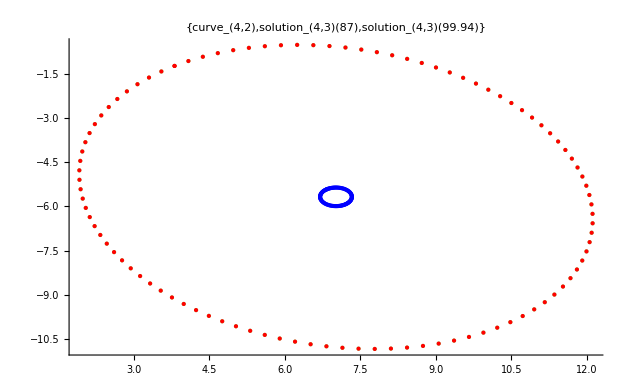

```mathematica
fgp[4,3,12.94]
```

```mathematica
equidist[4,3,40]
```

u-Bestimmungsdauer: 22.4574

```mathematica
fit[4,3,3]
```

4. Kurve, 3. Fit: Laenge nach Fluss: 1.983 , Laenge nach Fit: 1.983 , Abweichung: 0.000115039 %

4. Kurve(100.), 4. Evolution:   Laenge Anfangskurve = 1.983 , Laenge nach Fluss = 0.383752 , Berechnungsdauer = 0.060003

Gitterpunkte von NUMOL: 100

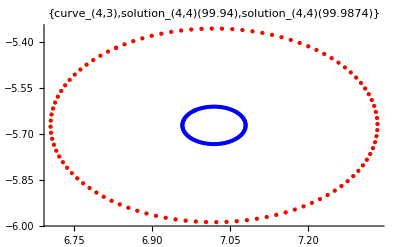

```mathematica
fgp[4,4,.0474]
```

```mathematica
equidist[4,4,40]
```

u-Bestimmungsdauer: 15.385

```mathematica
fit[4,4,1]
```

4. Kurve, 4. Fit: Laenge nach Fluss: 0.383752 , Laenge nach Fit: 0.383752 , Abweichung: 0.0000403996 %

4. Kurve(100.), 5. Evolution:   Laenge Anfangskurve = 0.383752 , Laenge nach Fluss = 0.216236 , Berechnungsdauer = 0.052003

Gitterpunkte von NUMOL: 100

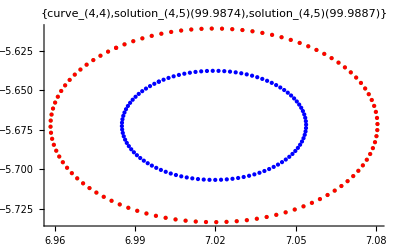

```mathematica
fgp[4,5,.00126]
```

```mathematica
equidist[4,5,20]
```

u-Bestimmungsdauer: 6.98444

```mathematica
fit[4,5,1]
```

4. Kurve, 5. Fit: Laenge nach Fluss: 0.216236 , Laenge nach Fit: 0.216236 , Abweichung: 4.21528×10^-6 %

4. Kurve(100.), 6. Evolution:   Laenge Anfangskurve = 0.216236 , Laenge nach Fluss = 0.0741581 , Berechnungsdauer = 0.040003

Gitterpunkte von NUMOL: 100

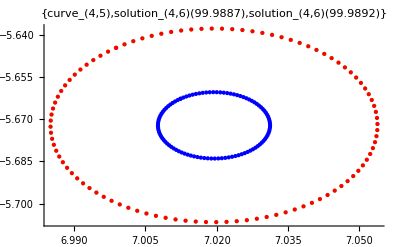

```mathematica
fgp[4,6,.000514]
```

#### 5. curve

5. Kurve(100.), 1. Evolution:   Laenge Anfangskurve = 130.819 , Laenge nach Fluss = 28.4642 , Berechnungsdauer = 0.220013

Gitterpunkte von NUMOL: 100

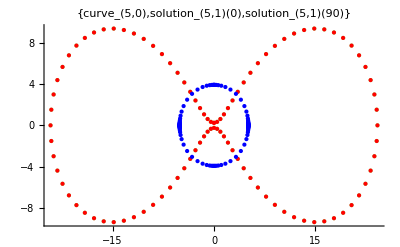

```mathematica
fgp[5,1,90]
```

```mathematica
equidist[5,1,80]
```

u-Bestimmungsdauer: 96.526

```mathematica
fit[5,1,8]
```

5. Kurve, 1. Fit: Laenge nach Fluss: 28.4642 , Laenge nach Fit: 28.4642 , Abweichung: 0.00004229 %

5. Kurve(100.), 2. Evolution:   Laenge Anfangskurve = 28.4642 , Laenge nach Fluss = 7.41121 , Berechnungsdauer = 0.100007

Gitterpunkte von NUMOL: 100

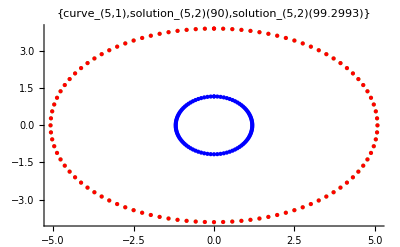

```mathematica
fgp[5,2,9.2993]
```

```mathematica
equidist[5,2,40]
```

u-Bestimmungsdauer: 21.1933

```mathematica
fit[5,2,3]
```

5. Kurve, 2. Fit: Laenge nach Fluss: 7.41121 , Laenge nach Fit: 7.41121 , Abweichung: 0.0000245108 %

5. Kurve(100.), 3. Evolution:   Laenge Anfangskurve = 7.41121 , Laenge nach Fluss = 1.12473 , Berechnungsdauer = 0.088006

Gitterpunkte von NUMOL: 100

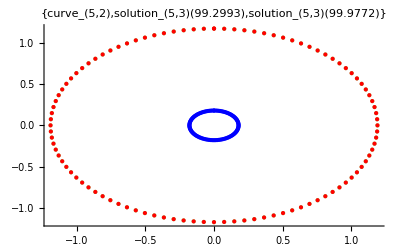

```mathematica
fgp[5,3,.677901]
```

```mathematica
equidist[5,3,20]
```

u-Bestimmungsdauer: 9.23658

```mathematica
fit[5,3,3]
```

5. Kurve, 3. Fit: Laenge nach Fluss: 1.12473 , Laenge nach Fit: 1.12473 , Abweichung: 0.000011387 %

5. Kurve(100.), 4. Evolution:   Laenge Anfangskurve = 1.12473 , Laenge nach Fluss = 0.508321 , Berechnungsdauer = 0.056003

Gitterpunkte von NUMOL: 100

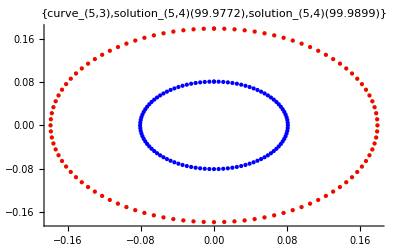

```mathematica
fgp[5,4,.0126999]
```

```mathematica
equidist[5,4,20]
```

u-Bestimmungsdauer: 7.37246

```mathematica
fit[5,4,1]
```

5. Kurve, 4. Fit: Laenge nach Fluss: 0.508321 , Laenge nach Fit: 0.508321 , Abweichung: 0.0000362285 %

5. Kurve(100.), 5. Evolution:   Laenge Anfangskurve = 0.508321 , Laenge nach Fluss = 0.0286042 , Berechnungsdauer = 0.084006

Gitterpunkte von NUMOL: 100

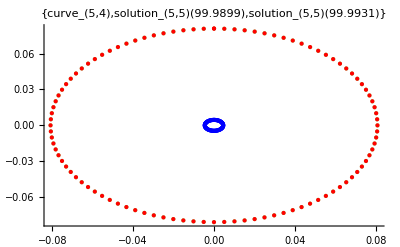

```mathematica
fgp[5,5,.00322]
```

#### 6. curve

6. Kurve(100.), 1. Evolution:   Laenge Anfangskurve = 123.348 , Laenge nach Fluss = 119.835 , Berechnungsdauer = 0.064004

Gitterpunkte von NUMOL: 100

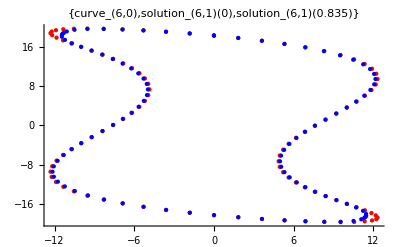

```mathematica
fgp[6,1,.835]
```

```mathematica
equidist[6,1,100]
```

u-Bestimmungsdauer: 57.9956

```mathematica
fit[6,1,18]
```

6. Kurve, 1. Fit: Laenge nach Fluss: 119.835 , Laenge nach Fit: 119.418 , Abweichung: 0.347842 %

6. Kurve(100.), 2. Evolution:   Laenge Anfangskurve = 119.418 , Laenge nach Fluss = 113.078 , Berechnungsdauer = 0.092006

Gitterpunkte von NUMOL: 100

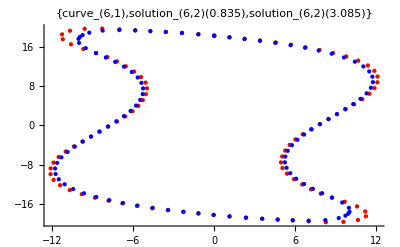

```mathematica
fgp[6,2,2.25]
```

```mathematica
equidist[6,2,100]
```

u-Bestimmungsdauer: 49.6191

```mathematica
fit[6,2,15]
```

6. Kurve, 2. Fit: Laenge nach Fluss: 113.078 , Laenge nach Fit: 112.91 , Abweichung: 0.148444 %

6. Kurve(100.), 3. Evolution:   Laenge Anfangskurve = 112.91 , Laenge nach Fluss = 71.7333 , Berechnungsdauer = 0.192012

Gitterpunkte von NUMOL: 100

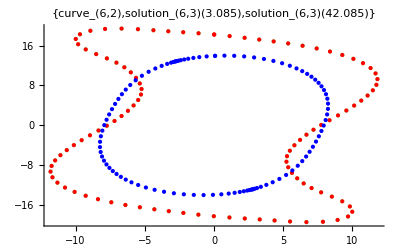

```mathematica
fgp[6,3,39]
```

```mathematica
equidist[6,3,80]
```

u-Bestimmungsdauer: 62.0279

```mathematica
fit[6,3,10]
```

6. Kurve, 3. Fit: Laenge nach Fluss: 71.7333 , Laenge nach Fit: 71.7316 , Abweichung: 0.00243303 %

6. Kurve(100.), 4. Evolution:   Laenge Anfangskurve = 71.7316 , Laenge nach Fluss = 26.8704 , Berechnungsdauer = 0.124007

Gitterpunkte von NUMOL: 100

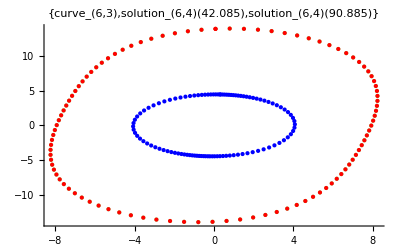

```mathematica
fgp[6,4,48.8]
```

```mathematica
equidist[6,4,50]
```

u-Bestimmungsdauer: 34.5942

```mathematica
fit[6,4,3]
```

6. Kurve, 4. Fit: Laenge nach Fluss: 26.8704 , Laenge nach Fit: 26.8705 , Abweichung: 0.000436058 %

6. Kurve(100.), 5. Evolution:   Laenge Anfangskurve = 26.8705 , Laenge nach Fluss = 9.33119 , Berechnungsdauer = 0.064004

Gitterpunkte von NUMOL: 100

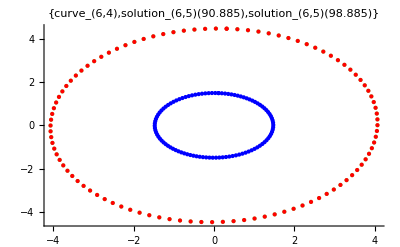

```mathematica
fgp[6,5,8.]
```

```mathematica
equidist[6,5,40]
```

u-Bestimmungsdauer: 19.1812

```mathematica
fit[6,5,3]
```

6. Kurve, 5. Fit: Laenge nach Fluss: 9.33119 , Laenge nach Fit: 9.33119 , Abweichung: 0.0000127092 %

6. Kurve(100.), 6. Evolution:   Laenge Anfangskurve = 9.33119 , Laenge nach Fluss = 1.67695 , Berechnungsdauer = 0.084005

Gitterpunkte von NUMOL: 100

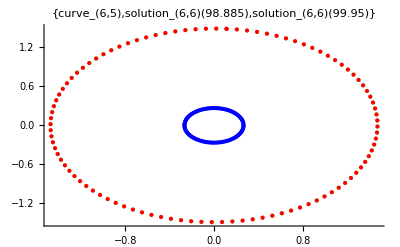

```mathematica
fgp[6,6,1.065]
```

```mathematica
equidist[6,6,20]
```

u-Bestimmungsdauer: 9.01656

```mathematica
fit[6,6,2]
```

6. Kurve, 6. Fit: Laenge nach Fluss: 1.67695 , Laenge nach Fit: 1.67695 , Abweichung: 0.000186864 %

6. Kurve(100.), 7. Evolution:   Laenge Anfangskurve = 1.67695 , Laenge nach Fluss = 0.718633 , Berechnungsdauer = 0.052003

Gitterpunkte von NUMOL: 100

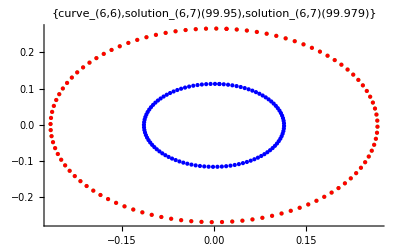

```mathematica
fgp[6,7,.02899]
```

```mathematica
equidist[6,7,20]
```

u-Bestimmungsdauer: 7.34846

```mathematica
fit[6,7,1]
```

6. Kurve, 7. Fit: Laenge nach Fluss: 0.718633 , Laenge nach Fit: 0.718629 , Abweichung: 0.000592146 %

6. Kurve(100.), 8. Evolution:   Laenge Anfangskurve = 0.718629 , Laenge nach Fluss = 0.0789802 , Berechnungsdauer = 0.092006

Gitterpunkte von NUMOL: 100

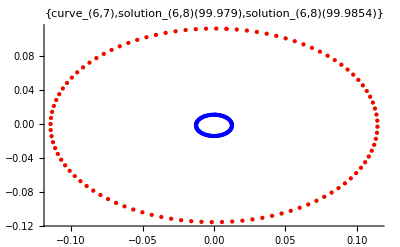

```mathematica
fgp[6,8,.0064]
```

#### Evolution plots

```mathematica
evoplot[3]
```

-Graphics3D-

### Evolution plots of lenght, area and isoperimetric ratio

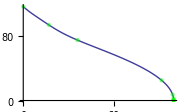
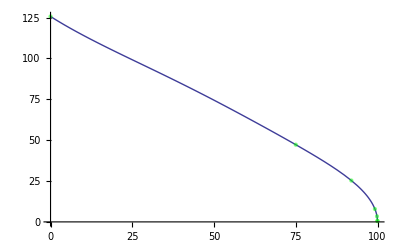
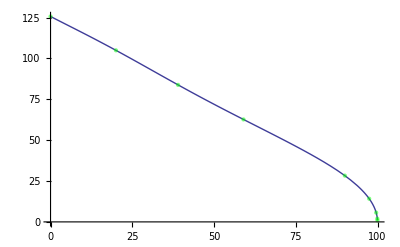

```mathematica
Table[Subscript[lplot, num],{num,1,3}]
```

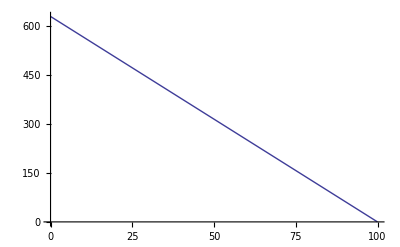
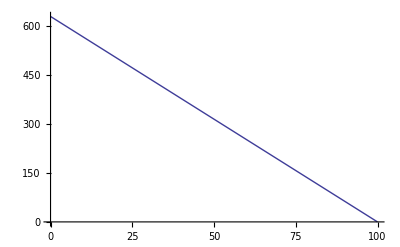
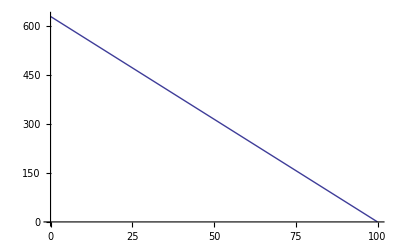

```mathematica
Table[Subscript[aplot, num],{num,1,3}]
```

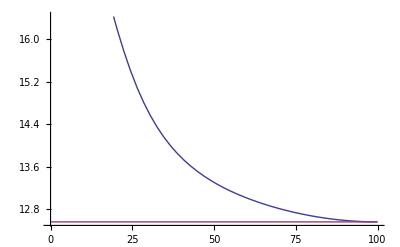
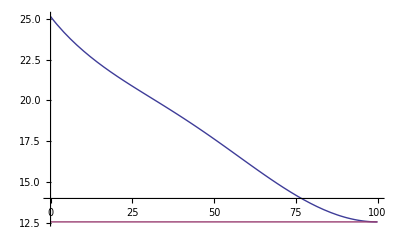
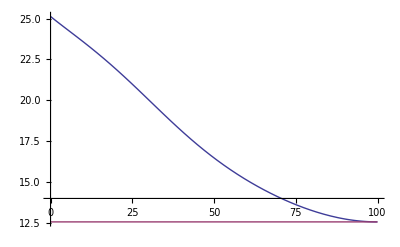

```mathematica
Table[Subscript[isoplot, num],{num,1,3}]
```

### Lenght, Area, Iso fits

```mathematica
Table[slength[num,Subscript[stepstop, num]],{num,1,noc}]
```

{0.0627594,0.0109139,0.0914559,0.0741581,0.0286042,0.0789802}

```mathematica
noc=6;isofit[num_,datapts_,order_]:=Fit[Join[Table[{i/datapts Subscript[te, num,Subscript[stepstop, num]],Subscript[length, num][i/datapts Subscript[te, num,Subscript[stepstop, num]]]^2/Subscript[area, num][i/datapts Subscript[te, num,Subscript[stepstop, num]]]},{i,0,datapts}],{{100,4π}}],Table[t^i,{i,0,order}],t];
Subscript[l, num_]:=Sqrt[Subscript[iso, num](Subscript[ao, num]-2π t)];
Do[Subscript[iso, num]=isofit[num,50,10],{num,1,noc}]
```

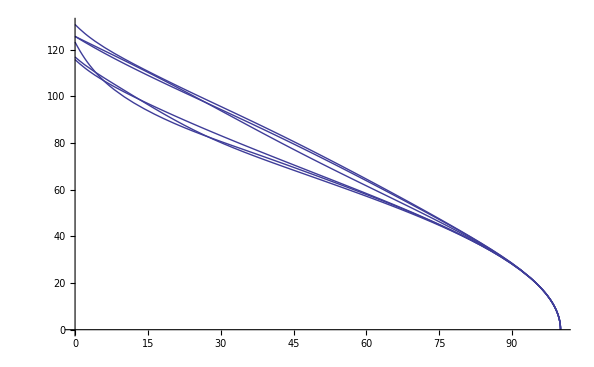

```mathematica
Plot[Table[Subscript[l, num],{num,1,noc}],{t,0,100}]
```

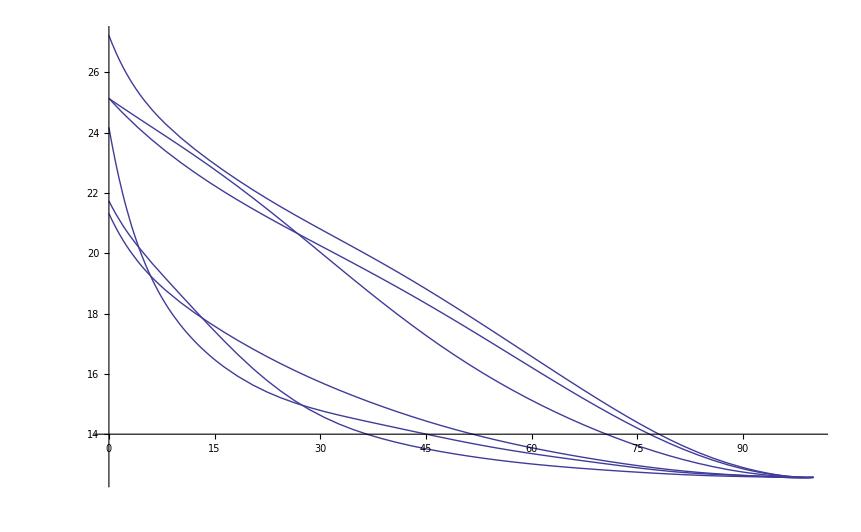

```mathematica
Plot[{Table[Subscript[iso, num],{num,1,noc}]},{t,0,100},PlotRange->Full]
```

### Partition function

```mathematica
noc=2;
z=Sum[Exp[-Subscript[iso, num](1+Subscript[c, num][t])],{num,1,noc}];
pde=Evaluate[D[z, t]] ==0;
bc=Table[Subscript[c, num][0]==0,{num,1,noc}];
```

```mathematica
zsol=DSolve[Join[{pde},bc],Table[Subscript[c, num][t],{num,1,noc}],t]
```

DSolve::underdet: There are more dependent variables than equations, so the system is underdetermined.

DSolve[{ⅇ^((-21.6388+0.460018 t-0.0082587 t^2+0.000408177 t^3-0.0000326113 t^4+1.23031×10^-6 t^5-2.49057×10^-8 t^6+2.93653×10^-10 t^7-2.02864×10^-12 t^8+7.63116×10^-15 t^9-1.20881×10^-17 t^10) (1+c_1[t])) ((0.460018-0.0165174 t+0.00122453 t^2-0.000130445 t^3+6.15157×10^-6 t^4-1.49434×10^-7 t^5+2.05557×10^-9 t^6-1.62291×10^-11 t^7+6.86804×10^-14 t^8-1.20881×10^-16 t^9) (1+c_1[t])+(-21.6388+0.460018 t-0.0082587 t^2+0.000408177 t^3-0.0000326113 t^4+1.23031×10^-6 t^5-2.49057×10^-8 t^6+2.93653×10^-10 t^7-2.02864×10^-12 t^8+7.63116×10^-15 t^9-1.20881×10^-17 t^10) c_1'[t])+ⅇ^((-25.0838+0.340811 t+0.000962282 t^2-0.000938838 t^3+0.0000552568 t^4-1.43617×10^-6 t^5+1.9549×10^-8 t^6-1.41827×10^-10 t^7+4.76109×10^-13 t^8-2.02059×10^-16 t^9-1.81608×10^-18 t^10) (1+c_2[t])) ((0.340811+0.00192456 t-0.00281651 t^2+0.000221027 t^3-7.18086×10^-6 t^4+1.17294×10^-7 t^5-9.92789×10^-10 t^6+3.80887×10^-12 t^7-1.81853×10^-15 t^8-1.81608×10^-17 t^9) (1+c_2[t])+(-25.0838+0.340811 t+0.000962282 t^2-0.000938838 t^3+0.0000552568 t^4-1.43617×10^-6 t^5+1.9549×10^-8 t^6-1.41827×10^-10 t^7+4.76109×10^-13 t^8-2.02059×10^-16 t^9-1.81608×10^-18 t^10) c_2'[t])==0,c_1[0]==0,c_2[0]==0},{c_1[t],c_2[t]},t]

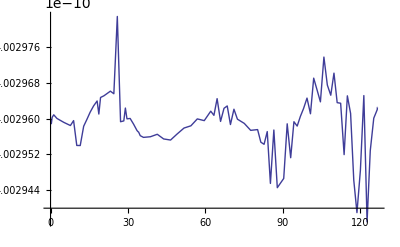

```mathematica
Plot[z/.zsol,{t,0,tmax}]
```